```mathematica
ClearAll;
Rx = 1/(√2)*({{√2, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, -1}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, √2, 0, 0}, {0, 1, 0, 0, 0, 1}, {0, 0, 1, 0, -1, 0}});
```

```mathematica
z6 = ConstantArray[0,{6,6}];
z3 = ConstantArray[0,{3,3}];
dim = 3 * 6;
Rxd = ArrayReshape[{Transpose[{Rx, z6,z6}],Transpose[{ z6, Rx,z6}],Transpose[{ z6 ,z6,Rx}]},{dim,dim}];
Rxd// MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(√2) | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(√2) | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | -1/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 1/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | -1/(√2) | 0)

```mathematica
adagQx= Transpose[Rxd].DiagonalMatrix[{1,1,1,1,1,1,0,1,1,0,-1,-1,1,1,1,1,1,1}].Rxd;
adagQx // MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
SvBm1 =1/Δ * ArrayReshape[{Transpose[{z3,z3}],Transpose[{z3, -IdentityMatrix[3]}]},{6,6}];
SvB0 = 1/Δ *ArrayReshape[{Transpose[{-IdentityMatrix[3],z3}],Transpose[{z3, IdentityMatrix[3]}]},{6,6}];
SvBp1 = 1/Δ *ArrayReshape[{Transpose[{IdentityMatrix[3],z3}],Transpose[{z3, z3}]},{6,6}];
SvBm1 // MatrixForm
SvB0 // MatrixForm
SvBp1 // MatrixForm
Sv = ArrayReshape[{Transpose[{ IdentityMatrix[6], z6 , z6}], Transpose[{SvBm1*Exp[-ⅈ*k*Δ*(-1)],SvB0, SvBp1*Exp[-ⅈ*k*Δ*(1)]}], Transpose[{z6, z6,IdentityMatrix[6]}]},{dim,dim}];
(*StencilP=1/Δ*{-1/2,0,1/2};
StencilM=1/Δ*{-1/2,0,1/2};
SvUpper= ArrayReshape[{{IdentityMatrix[3],z3}^ᵀ,{z3, z3}^ᵀ},{6,6}];
SvLower = ArrayReshape[{{z3,z3}^ᵀ,{z3, IdentityMatrix[3]}^ᵀ},{6,6}];
Sv =ConstantArray[0,{30,30}]; 
Sv[[1;;6, 1;;6]] = IdentityMatrix[6];
Sv[[25;;30, 25;;30]] = IdentityMatrix[6];
For[i=1,i<4,i=i+1,For[j=0+i-1,j<3+i-1,j=j+1,Sv[[i*6+1;;i*6+5+1,j*6+1;;j*6+5+1]]=SvUpper*StencilM[[j+2-i]] + SvLower*StencilP[[j+2-i]]]]*)
Svk[k_] = Sv;
MatrixForm[Svk[k]]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/Δ | 0 | 0
0 | 0 | 0 | 0 | -1/Δ | 0
0 | 0 | 0 | 0 | 0 | -1/Δ)

(-1/Δ | 0 | 0 | 0 | 0 | 0
0 | -1/Δ | 0 | 0 | 0 | 0
0 | 0 | -1/Δ | 0 | 0 | 0
0 | 0 | 0 | 1/Δ | 0 | 0
0 | 0 | 0 | 0 | 1/Δ | 0
0 | 0 | 0 | 0 | 0 | 1/Δ)

(1/Δ | 0 | 0 | 0 | 0 | 0
0 | 1/Δ | 0 | 0 | 0 | 0
0 | 0 | 1/Δ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/Δ | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ k Δ)/Δ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/Δ | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ k Δ)/Δ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/Δ | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ k Δ)/Δ | 0 | 0 | 0
0 | 0 | 0 | -ⅇ^(ⅈ k Δ)/Δ | 0 | 0 | 0 | 0 | 0 | 1/Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅇ^(ⅈ k Δ)/Δ | 0 | 0 | 0 | 0 | 0 | 1/Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅇ^(ⅈ k Δ)/Δ | 0 | 0 | 0 | 0 | 0 | 1/Δ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
step[k_] = adagQx.Transpose[Rxd].Svk[k].Rxd;
step[k] // MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(ⅈ k Δ)/(2 Δ) | 0 | 0 | 0 | ⅇ^(ⅈ k Δ)/(2 Δ) | 0 | -1/Δ | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ k Δ)/(2 Δ) | 0 | 0 | 0 | -ⅇ^(-ⅈ k Δ)/(2 Δ)
0 | 0 | ⅇ^(ⅈ k Δ)/(2 Δ) | 0 | -ⅇ^(ⅈ k Δ)/(2 Δ) | 0 | 0 | 0 | -1/Δ | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ k Δ)/(2 Δ) | 0 | ⅇ^(-ⅈ k Δ)/(2 Δ) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅇ^(ⅈ k Δ)/(2 Δ) | 0 | ⅇ^(ⅈ k Δ)/(2 Δ) | 0 | 0 | 0 | 0 | 0 | -1/Δ | 0 | 0 | 0 | ⅇ^(-ⅈ k Δ)/(2 Δ) | 0 | ⅇ^(-ⅈ k Δ)/(2 Δ) | 0
0 | ⅇ^(ⅈ k Δ)/(2 Δ) | 0 | 0 | 0 | ⅇ^(ⅈ k Δ)/(2 Δ) | 0 | 0 | 0 | 0 | 0 | -1/Δ | 0 | -ⅇ^(-ⅈ k Δ)/(2 Δ) | 0 | 0 | 0 | ⅇ^(-ⅈ k Δ)/(2 Δ)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

{{w[k]→-ⅈ},{w[k]→-ⅈ},{w[k]→-ⅈ},{w[k]→-ⅈ},{w[k]→-ⅈ},{w[k]→-ⅈ},{w[k]→-ⅈ},{w[k]→-ⅈ},{w[k]→-ⅈ},{w[k]→-ⅈ},{w[k]→-ⅈ},{w[k]→-ⅈ},{w[k]→2 ⅈ},{w[k]→2 ⅈ},{w[k]→2 ⅈ},{w[k]→2 ⅈ}}

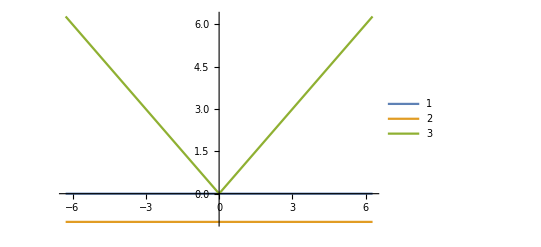

```mathematica
Δ = 1/2;
Element[k,Reals];
wsol[k_] = Simplify[Solve[Det[-ⅈ*w[k]*IdentityMatrix[dim] + step[k]]==0 && w[k]!=0 ,w[k], Complexes]]
w1[k_]= w[k]/.wsol[k][[12]];
Plot[{Re[w1[k]], Im[w1[k]],Abs[k]},{k,-π*2,π*2},PlotLegends->{"1","2","3"}]
```

```mathematica
{val[k_], vec[k_]} = Eigensystem[step[k]];
ArrayReshape[vec[k],{dim,3,6}]
val[k_]
```

{{{0,0,0,0,0,0},{0,0,0,1,0,0},{0,0,0,0,0,0}},{{0,0,0,0,0,0},{1,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,0,0}},{{0,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,0}},{{0,0,0,0,0,0},{0,0,1,0,0,0},{0,0,0,0,0,0}},{{0,0,0,0,0,0},{0,1,0,0,0,0},{0,0,0,0,0,0}},{{0,-ⅇ^(-ⅈ k),0,0,0,0},{0,-2/3 ⅇ^(-(ⅈ k)/2),0,0,0,0},{0,0,0,0,0,1}},{{0,0,ⅇ^(-ⅈ k),0,0,0},{0,0,2/3 ⅇ^(-(ⅈ k)/2),0,0,0},{0,0,0,0,1,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,0,0}},{{0,0,ⅇ^(-ⅈ k),0,0,0},{0,0,2/3 ⅇ^(-(ⅈ k)/2),0,0,0},{0,0,1,0,0,0}},{{0,ⅇ^(-ⅈ k),0,0,0,0},{0,2/3 ⅇ^(-(ⅈ k)/2),0,0,0,0},{0,1,0,0,0,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{1,0,0,0,0,0}},{{0,3 ⅇ^(-(ⅈ k)/2),0,0,0,0},{0,1,0,0,0,1},{0,0,0,0,0,0}},{{0,0,-3 ⅇ^(-(ⅈ k)/2),0,0,0},{0,0,-1,0,1,0},{0,0,0,0,0,0}},{{0,-1,0,0,0,1},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,1,0,1,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{1,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}}

{0,0,-2,-2,-2,-2,1,1,1,1,1,1,1,1,1,1,1,1}